```mathematica
Clear["Global`*"]
Subscript[σ, sl]=1; Subscript[σ, lg]=2; Subscript[σ, sg]=3;

A={{1,1/2,1/2},{1/2,1,1/2},{1/2,1/2,1}}
d=0.01;
(*fs[x_,y_]:=0.5*(1-Tanh[x/d]);
fl[x_,y_]:=(1-fs[x,y])*0.5*(1+Tanh[(x^2+y^2-1)/d]);*)
(*fs[x_,y_]:=If[x>0,0,1];
fl[x_,y_]:=If[x>0,If[x^2+y^2>1,1,0],0];*)
fg[x_,y_]:=1-fs[x,y]-fl[x,y]
```

{{1,1/2,1/2},{1/2,1,1/2},{1/2,1/2,1}}

```mathematica
X={fl[x,y]+fg[x,y],fg[x,y]+fs[x,y],fl[x,y]+fs[x,y]}
```

{1-fs[x,y],1-fl[x,y],fl[x,y]+fs[x,y]}

```mathematica
LinearSolve[A,{1,0,0}]
```

{3/2,-1/2,-1/2}

```mathematica
B=Inverse[A]
```

{{3/2,-1/2,-1/2},{-1/2,3/2,-1/2},{-1/2,-1/2,3/2}}

```mathematica
FullSimplify[B.X]
(*fun[fl_,fs_]:={1-2 fs,1-2 fl,-1+2 fl+2 fs}*)
```

{1-2 fs[x,y],1-2 fl[x,y],-1+2 fl[x,y]+2 fs[x,y]}

```mathematica
fun[1/3,1/3]
```

fun[1/3,1/3]

```mathematica
fun[fl,sd]
```

fun[fl,sd]

```mathematica
fs
```

fs

```mathematica
Plot3D[{fs[x,y], fl[x,y], fg[x,y]},{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[{(fl[x,y]+fg[x,y]),(fg[x,y]+fs[x,y]),(fl[x,y]+fs[x,y])},{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[{1-2 fs[x,y],1-2 fl[x,y],-1+2 fl[x,y]+2 fs[x,y]},{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[{fl[x,y]+fg[x,y](*,fg[x,y]+fs[x,y],fl[x,y]+fs[x,y]*)},{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
A={{1,1,0,0},{1,0,1,0},{1,0,0,1},{0,1,1,0},{0,1,0,1},{0,0,1,1}}
b = {Subscript[σ, 12],Subscript[σ, 13],Subscript[σ, 14],Subscript[σ, 23],Subscript[σ, 24],Subscript[σ, 34]}
xs = {Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3],Subscript[σ, 4]}
LinearSolve[A,b]
```

{{1,1,0,0},{1,0,1,0},{1,0,0,1},{0,1,1,0},{0,1,0,1},{0,0,1,1}}

{σ_12,σ_13,σ_14,σ_23,σ_24,σ_34}

{σ_1,σ_2,σ_3,σ_4}

{}

```mathematica
A={{1,1,0},{1,0,1},{0,1,1}}
b = {Subscript[σ, 12],Subscript[σ, 13],Subscript[σ, 23]}
LinearSolve[A,b]
```

{{1,1,0},{1,0,1},{0,1,1}}

{σ_12,σ_13,σ_23}

{1/2 (σ_12+σ_13-σ_23),1/2 (σ_12-σ_13+σ_23),1/2 (-σ_12+σ_13+σ_23)}

```mathematica
DSolve[ρ*y'[x]==-PL+mu1*D[ Exp[a^2*(y-L0)^2/(L0)^2]*y'[x]],y[x],y]
```

DSolve::alliv: The function y[x] was specified without dependence on all the independent variables. Each function must depend on all the independent variables.

DSolve[ρ y'[x]==-PL+ⅇ^((a^2 (-L0+y)^2)/L0^2) mu1 y'[x],y[x],y]

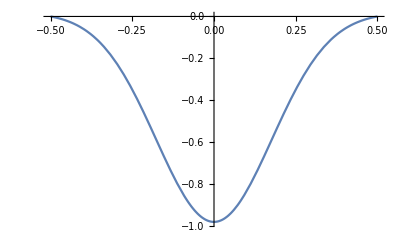

```mathematica
Plot[Exp[-4]-Exp[-16*x*x],{x,-0.5,0.5}]
```

```mathematica
PL=1; a=2; L0=1;mu1=1;
DSolve[PL==+mu1*D[ Exp[a^2*(y-L0)^2/(L0)^2]*u'[y], y],u[y],u]
```

DSolve::alliv: The function u[y] was specified without dependence on all the independent variables. Each function must depend on all the independent variables.

DSolve[1==8 ⅇ^(4 (-1+y)^2) (-1+y) u'[y]+ⅇ^(4 (-1+y)^2) u''[y],u[y],u]

```mathematica
ClearAll[PL,a,L0,mu1]
DSolve[{PL==+mu1*D[ Exp[a^2*(x-L0)^2/(L0)^2]*y'[x], x], y[-L0/2]==0,y[L0/2]==0},y[x],x]
```

{{y[x]→-((ⅇ^(-(9 a^2)/4) L0^2 PL (-Erf[a/2]+ⅇ^((5 a^2)/4+(a^2 (2 L0-x) x)/L0^2) Erf[a/2]+ⅇ^(2 a^2) Erf[(3 a)/2]-ⅇ^((5 a^2)/4+(a^2 (2 L0-x) x)/L0^2) Erf[(3 a)/2]-Erf[(a (-L0+x))/L0]+ⅇ^(2 a^2) Erf[(a (-L0+x))/L0]))/(2 a^2 mu1 (Erf[a/2]-Erf[(3 a)/2])))}}